```mathematica
SetDirectory[NotebookDirectory[]]; 
rawFresnelDiffuseReflectance = BinaryReadList["./BRDF0_64x64.table",{"Real32", "Real32"}]
```

{{0.825424,0.174544},{0.82543,0.174547},{0.825458,0.174422},{0.825487,0.173973},{0.825505,0.173053},{0.825503,0.171715},{0.825467,0.170027},{0.825382,0.168053},{0.825226,0.165818},{0.82498,0.163364},{0.824624,0.160729},{0.824133,0.157913},{0.823486,0.154964},{0.82266,0.151886},{0.821637,0.148725},{0.820398,0.145485},{0.818928,0.142204},{0.817213,0.138893},{0.815239,0.135558},{0.813002,0.132234},{0.810494,0.128923},{0.807716,0.125642},{0.804663,0.122393},{0.801341,0.119205},{0.79781,0.116081},{0.794068,0.113021},{0.790106,0.110044},{0.785908,0.107146},{0.781479,0.104321},{0.776827,0.101569},{0.771966,0.0989047},{0.766908,0.0963139},{0.761662,0.0937962},{0.756246,0.0913586},{0.750688,0.0889967},{0.744996,0.0867054},{0.739181,0.0844877},{0.733248,0.0823448},{0.727209,0.0802761},{0.721099,0.078274},{0.71493,0.0763353},{0.708694,0.0744569},{0.70239,0.0726441},{0.696018,0.0708902},{0.689603,0.0691922},{0.683192,0.0675534},{0.676786,0.0659675},{0.670362,0.0644396},{0.663911,0.0629606},{0.657458,0.0615314},{0.651014,0.0601449},{0.64459,0.0588049},{0.638177,0.0575022},{0.631769,0.0562424},{0.625376,0.0550223},{0.619054,0.053844},{0.612794,0.0527078},{0.606561,0.0516089},{0.600354,0.0505446},{0.594191,0.0495116},{0.588076,0.0485097},{0.582011,0.0475359},{0.575997,0.0465922},{0.570021,0.0456732}}

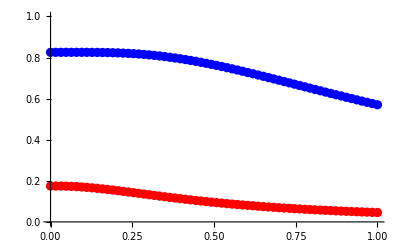

```mathematica
FresnelDiffuseReflectance0 = Table[{(x-1)/63,rawFresnelDiffuseReflectance[[x]][[1]]}, {x,1,64}];
FresnelDiffuseReflectance1 = Table[{(x-1)/63,rawFresnelDiffuseReflectance[[x]][[2]]}, {x,1,64}];
Show[ 
ListPlot[FresnelDiffuseReflectance1,PlotRange->{0,1},PlotStyle->Red],
ListPlot[FresnelDiffuseReflectance0,PlotStyle->Blue]
]
```

```mathematica
fittingMethod="Automatic";
```

Function[x,0.831387+0.000403213 x-0.276223 x^2]

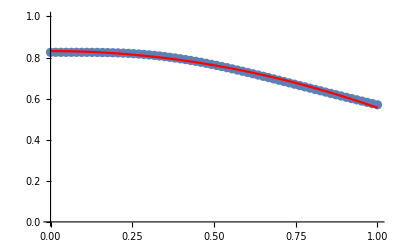

```mathematica
model0=a+b*x+c*x^2+d*x^3+e*x^4;
model0=a+b*x+c*x^2+d*x^3;
model0=a+b*x+c*x^2;
(*model0=a+b*x;*)
fittingReflectance0 = FindFit[FresnelDiffuseReflectance0,model0,{a,b,c,d,e},x,Method->fittingMethod];
model0 =Function[x,Evaluate[ model0/.fittingReflectance0]]
Show[
ListPlot[FresnelDiffuseReflectance0,PlotRange->{0,1}],
Plot[model0[x],{x,0,1},PlotStyle->Red]
]
```

Function[x,0.188237-0.218206 x+0.0727132 x^2]

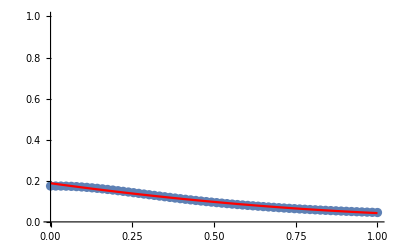

```mathematica
model1=a+b*x+c*x^2+d*x^3+e*x^4;
model1=a+b*x+c*x^2+d*x^3;
model1=a+b*x+c*x^2;
(*model1=a+b*x;*)
fittingReflectance1 = FindFit[FresnelDiffuseReflectance1,model1,{a,b,c,d,e},x,Method->fittingMethod];
model1 =Function[x,Evaluate[ model1/.fittingReflectance1]]
Show[
ListPlot[FresnelDiffuseReflectance1,PlotRange->{0,1}],
Plot[model1[x],{x,0,1},PlotStyle->Red]
]
```